1

45.2844

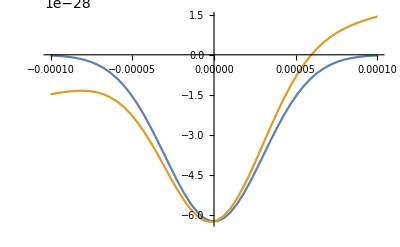

```mathematica
c = 3*10^8;
ϵ0 = 8.85*10^-12;
kB = 1.38*10^-23;
a0 = .52*10^-10;
m = 88*1.66*10^-27;
α = 300*4π ϵ0 a0^3 (* polarizability of ground state *);
P = 1
w = 60*10^-6;
λ = 515*10^-9;
g = 10;
U0trap= (4 α P)/(ϵ0*c*π*w^2);
Utrap = -U0trap*Exp[-2 r^2/w^2];
trapdepthuK = 10^6 U0trap/kB
ωrad = 2 √(Utrap/(w^2 m));
frad = ωrad/(2π);
Plot[{Utrap, Utrap+ m*g*r}, {r, -.0001, .0001}]
```